```mathematica
S[x_]:=Exp[-Abs[x]/2]
Subscript[k, w][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](x-ξ)],x<ξ}}]
Subscript[k, l][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](x-ξ)],x<ξ}}]
var=Rationalize[{Subscript[α, w]->50.58,Subscript[β, w]->3.85/0.38,Subscript[η, w]->1/(0.38*10)*Q,Subscript[α, l]->192.2/(1.89*10),Subscript[β, l]->3.85/1.89,Subscript[η, l]->1/(1.89*10)*Q,Subscript[a, 0]->0.6,Subscript[a, 1]->0.38,M->0.38/1.89,Subscript[L, 0]->-1+ϵ,Subscript[L, 1]->1+ϵ}];
```

```mathematica
Subscript[T, 0][ξ_]:=Limit[Subscript[c, 0] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ<Subscript[A, 0]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,-∞,Subscript[A, 0]},Assumptions->ξ<Subscript[A, 0]<Subscript[L, 0]/.var]+Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,-∞,Subscript[A, 0]},Assumptions->ξ<Subscript[A, 0]<Subscript[L, 0]/.var]
Subscript[F, 0][ξ_]=Refine[Subscript[T, 0][ξ]/.var,{0<ϵ<1,ξ<Subscript[A, 0]<0}];
```

```mathematica
Subscript[T, 1][ξ_]:=Limit[Subscript[c, 2] Subscript[k, w][x,ξ]-Subscript[c, 1] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 0],Assumptions->ξ<Subscript[L, 0]]-Limit[Subscript[c, 0] Subscript[k, w][x,ξ]+ D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ>Subscript[A, 0]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[A, 0],Subscript[L, 0]}/.var,Assumptions->{Subscript[A, 0]<ξ<Subscript[L, 0]/.var,Subscript[A, 0]<Subscript[L, 0]/.var}]+Subscript[η, w](1-Subscript[a, 1])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[A, 0],Subscript[L, 0]}/.var,Assumptions->{Subscript[A, 0]<ξ<Subscript[L, 0]/.var,Subscript[A, 0]<Subscript[L, 0]/.var}]
Subscript[F, 1][ξ_]=Refine[Subscript[T, 1][ξ]/.var,{0<ϵ<1,Subscript[A, 0]<ξ<Subscript[L, 0]<0}/.var];
```

```mathematica
Subscript[T, 2][ξ_]:=Limit[Subscript[c, 3] Subscript[k, l][x,ξ],x->Subscript[B, 0],Assumptions->ξ<Subscript[B, 0]]-
Limit[M Subscript[c, 2] Subscript[k, l][x,ξ]-Subscript[c, 1] D[Subscript[k, l][x,ξ], x],x->Subscript[L, 0],Assumptions->ξ>Subscript[L, 0]]-
Subscript[α, l] Integrate[Subscript[k, l][x,ξ],{x,Subscript[L, 0],Subscript[B, 0]}/.var,Assumptions->Subscript[B, 0]>Subscript[L, 0]/.var]+
Subscript[η, l](1-Subscript[a, 0])Integrate[Subscript[k, l][x,ξ]S[x],{x,Subscript[L, 0],Subscript[B, 0]}/.var,Assumptions->Subscript[B, 0]>Subscript[L, 0]/.var]
Subscript[F, 2][ξ_]=Refine[Subscript[T, 2][ξ]/.var,{0<ϵ<1,Subscript[L, 0]<ξ<Subscript[B, 0]<0}/.var];
```

```mathematica
Subscript[T, 3][ξ_]:=Limit[Subscript[c, 4] Subscript[k, l][x,ξ],x->Subscript[B, 1],Assumptions->ξ<Subscript[B, 1]]-
Limit[Subscript[c, 3] Subscript[k, l][x,ξ],x->Subscript[B, 0],Assumptions->ξ>Subscript[B, 0]]-
Subscript[α, l] Integrate[Subscript[k, l][x,ξ],{x,Subscript[B, 0],Subscript[B, 1]}/.var,Assumptions->Subscript[B, 0]<Subscript[B, 1]]+
Subscript[η, l](1-Subscript[a, 1])Integrate[Subscript[k, l][x,ξ]S[x],{x,Subscript[B, 0],Subscript[B, 1]}/.var,Assumptions->Subscript[B, 0]<Subscript[B, 1]]
Subscript[F, 3][ξ_]=Refine[Subscript[T, 3][ξ]/.var,{0<ϵ<1,Subscript[B, 0]<ξ<Subscript[B, 1],Subscript[B, 0]<0,Subscript[B, 1]>1}];
```

```mathematica
Subscript[T, 4][ξ_]:=Limit[M Subscript[c, 6] Subscript[k, l][x,ξ]-Subscript[c, 5] D[Subscript[k, l][x,ξ], x],x->Subscript[L, 1],Assumptions->ξ<Subscript[L, 1]]-
Limit[Subscript[c, 4] Subscript[k, l][x,ξ],x->Subscript[B, 1],Assumptions->ξ>Subscript[B, 1]]-
Subscript[α, l] Integrate[Subscript[k, l][x,ξ],{x,Subscript[B, 1],Subscript[L, 1]}/.var,Assumptions->Subscript[B, 1]<Subscript[L, 1]/.var]+
Subscript[η, l](1-Subscript[a, 0])Integrate[Subscript[k, l][x,ξ]S[x],{x,Subscript[B, 1],Subscript[L, 1]}/.var,Assumptions->Subscript[B, 1]<Subscript[L, 1]/.var]
Subscript[F, 4][ξ_]=Refine[Subscript[T, 4][ξ]/.var,{0<ϵ<1,0<Subscript[B, 1]<ξ<Subscript[L, 1]}/.var];
```

```mathematica
Subscript[T, 5][ξ_]:=-Limit[Subscript[c, 6] Subscript[k, w][x,ξ]-Subscript[c, 5] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 1],Assumptions->ξ>Subscript[L, 1]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[L, 1],∞}/.var,Assumptions->ξ>Subscript[L, 1]/.var]+Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[L, 1],∞}/.var,Assumptions->ξ>Subscript[L, 1]/.var]
Subscript[F, 5][ξ_]=Refine[Subscript[T, 5][ξ]/.var,{0<ϵ<1,Subscript[L, 1]<ξ}/.var];
```

```mathematica
Subscript[eqn, 0]=Subscript[F, 0][Subscript[A, 0]]+1==0;
Subscript[eqn, 1]=Subscript[F, 1][Subscript[A, 0]]+1==0;
Subscript[eqn, 2]=Subscript[F, 2][Subscript[B, 0]]==0;
Subscript[eqn, 3]=Subscript[F, 3][Subscript[B, 0]]==0;
Subscript[eqn, 4]=Subscript[F, 3][Subscript[B, 1]]==0;
Subscript[eqn, 5]=Subscript[F, 4][Subscript[B, 1]]==0;
Subscript[eqn, 6]=Subscript[F, 2]'[Subscript[L, 0]]-M Subscript[F, 1]'[Subscript[L, 0]]==0/.var;
Subscript[eqn, 7]=Subscript[F, 4]'[Subscript[L, 1]]-M Subscript[F, 5]'[Subscript[L, 1]]==0/.var;
Subscript[eqn, 8]=Subscript[F, 2][Subscript[L, 0]]-Subscript[F, 1][Subscript[L, 0]]==0/.var;
Subscript[eqn, 9]=Subscript[F, 4][Subscript[L, 1]]-Subscript[F, 5][Subscript[L, 1]]==0/.var;
```

```mathematica
Beep[]
```

```mathematica
(*Finding what Q's has solution on this form*)
Subscript[Q, min]=486;
Subscript[Q, max]=490;
n=2(Subscript[Q, max]-Subscript[Q, min])+1;
(*n=1401;*)
Subscript[ϵ, test]=0.05;
sols={};
Monitor[
For[i=0,i<n,i++,
tempQ={Q->Rationalize[Subscript[Q, min]+(Subscript[Q, max]-Subscript[Q, min])*i/(n-1),0],ϵ->Rationalize[Subscript[ϵ, test],0]};
sol=Quiet[FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5],Subscript[eqn, 6],Subscript[eqn, 7],Subscript[eqn, 8],Subscript[eqn, 9]}/.tempQ,{{Subscript[c, 0],0},{Subscript[c, 1],0},{Subscript[c, 2],0},{Subscript[c, 3],0},{Subscript[c, 4],0},{Subscript[c, 5],0},{Subscript[c, 6],0},{Subscript[A, 0],-1.5},{Subscript[B, 0],-0.1},{Subscript[B, 1],0.1}}/.tempQ,MaxIterations->1000,WorkingPrecision->30]];
sol=Join[sol,tempQ,var/.tempQ];
Quiet[conds=Subscript[A, 0]<Subscript[L, 0]<Subscript[B, 0]<Subscript[B, 1]<Subscript[L, 1]&&
NMaxValue[{Subscript[F, 0][x],-10<x<Subscript[A, 0]}/.sol,x]<-0.99999&&
NMinValue[{Subscript[F, 1][x],Subscript[A, 0]<x<Subscript[L, 0]}/.sol,x]>-1.00001&&
NMaxValue[{Subscript[F, 2][x],Subscript[L, 0]<x<Subscript[B, 0]}/.sol,x]<0.00001&&
NMinValue[{Subscript[F, 3][x],Subscript[B, 0]<x<Subscript[B, 1]}/.sol,x]>-0.00001&&
NMaxValue[{Subscript[F, 4][x],Subscript[B, 1]<x<Subscript[L, 1]}/.sol,x]<0.00001&&
NMaxValue[{Subscript[F, 5][x],Subscript[L, 1]<x<10}/.sol,x]<-0.99999/.sol];
If[conds,M[x_]=Rationalize[Piecewise[{{Subscript[F, 0][x],x<=Subscript[A, 0]},{Subscript[F, 1][x],Subscript[A, 0]<x<Subscript[L, 0]},{Subscript[F, 2][x],Subscript[L, 0]<=x<Subscript[B, 0]},{Subscript[F, 3][x],Subscript[B, 0]<=x<=Subscript[B, 1]},{Subscript[F, 4][x],Subscript[B, 1]<x<=Subscript[L, 1]},{Subscript[F, 5][x],Subscript[L, 1]<x}}/.sol],0];points=Table[-10+0.01(i-1),{i,2001}];
nSolution=N[Round[Map[M, points],10^-10]];sols=Join[sols,{{N[Round[Q/.sol,10^-10]],N[Round[NMaxValue[{M[x],Subscript[L, 0]<x<Subscript[L, 1]}/.sol,x],10^-10]],N[Round[M[0]/.sol,10^-10]],N[Round[M[Subscript[ϵ, test]]/.sol,10^-10]],nSolution}}],Nothing];
],{N[i/n],N[Q/.tempQ]}]
Beep[]
```

```mathematica
Export["/home/ask/Documents/masterA/Code/Big Project/0.05/4B - IceWaterSnowLandSnowIce2.csv",sols,Format->Table];
```

{c_0→4.8472266858705868031,c_1→-0.082038904126189645213,c_2→4.4377020974508719713,c_3→1.1716252480419311588,c_4→-2.0573770943829949596,c_5→-1.0046539744810202249,c_6→-4.4252125501201521536,A_0→-1.1510141732681835007,B_0→-0.87054736659541694163,B_1→0.37809971419415024563}

True 0. True

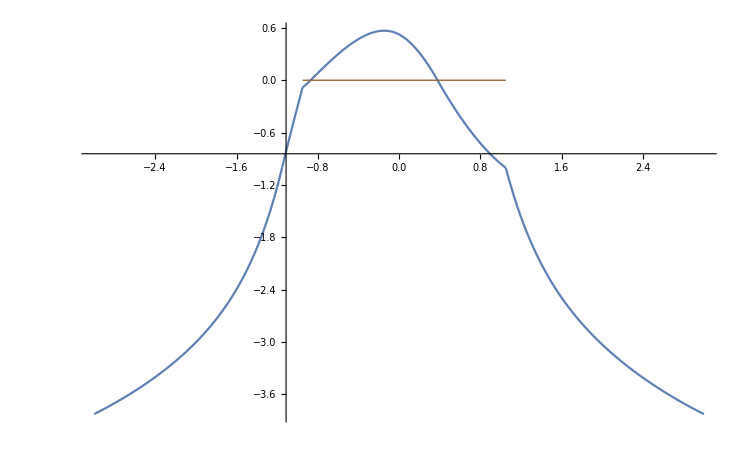

```mathematica
(* Finding particular solution *)
tempQ={Q->Rationalize[489,0],ϵ->Rationalize[0.05,0]};
sol=FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5],Subscript[eqn, 6],Subscript[eqn, 7],Subscript[eqn, 8],Subscript[eqn, 9]}/.tempQ,{{Subscript[c, 0],0},{Subscript[c, 1],0},{Subscript[c, 2],0},{Subscript[c, 3],0},{Subscript[c, 4],0},{Subscript[c, 5],0},{Subscript[c, 6],0},{Subscript[A, 0],-1.5},{Subscript[B, 0],-0.1},{Subscript[B, 1],0.1}},MaxIterations->1000,WorkingPrecision->20]
sol=Join[Rationalize[sol,0],tempQ,var/.tempQ];
(* Plotting solution *)
Subscript[p, 0]=Plot[Subscript[F, 0][x]/.sol,{x,-3,Subscript[A, 0]}/.sol,PlotRange->All,WorkingPrecision->20];
Subscript[p, 1]=Plot[Subscript[F, 1][x]/.sol,{x,Subscript[A, 0],Subscript[L, 0]}/.sol,PlotRange->All,WorkingPrecision->20];
Subscript[p, 2]=Plot[Subscript[F, 2][x]/.sol,{x,Subscript[L, 0],Subscript[B, 0]}/.sol,PlotRange->All,WorkingPrecision->20];
Subscript[p, 3]=Plot[Subscript[F, 3][x]/.sol,{x,Subscript[B, 0],Subscript[B, 1]}/.sol,PlotRange->All,WorkingPrecision->20];
Subscript[p, 4]=Plot[Subscript[F, 4][x]/.sol,{x,Subscript[B, 1],Subscript[L, 1]}/.sol,PlotRange->All,WorkingPrecision->20];
Subscript[p, 5]=Plot[Subscript[F, 5][x]/.sol,{x,Subscript[L, 1],3}/.sol,PlotRange->All,WorkingPrecision->20];
Subscript[p, 6]=Plot[0,{x,Subscript[L, 0],Subscript[L, 1]}/.sol,PlotRange->All,PlotStyle->{Brown,Thick}];
Print[Subscript[F, 1][Subscript[L, 0]]<0/.sol," ",NMaxValue[{Subscript[F, 4][x],Subscript[B, 1]<x<Subscript[L, 1]}/.sol,x]," ",Subscript[F, 4][Subscript[L, 1]]<-1/.sol]
Show[Subscript[p, 0],Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[p, 5],Subscript[p, 6],PlotRange->All]
```